# Bee Communication

## In collaboration with Seth Bullock February 2025

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
d="/Users/edizquie/Documents/GitHub/BeeCommunication/src_analysis/";
```

```mathematica
r = "40";
```

## Evolution

```mathematica
e=Transpose[Import[d<>"evol_"<>r<>".dat"]];
```

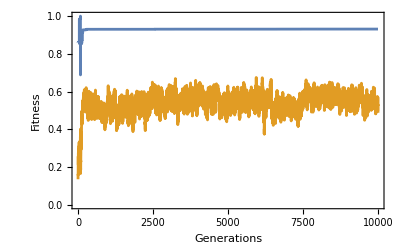

```mathematica
ListLinePlot[{e[[2]],e[[3]]},Frame->True,FrameLabel->{"Generations","Fitness"}]
```

## Behavior

```mathematica
S1E1P1=Import[d<>"behavior_Signaler_"<>r<>"_Env1_Phase1.dat"];
S1E1P2=Import[d<>"behavior_Signaler_"<>r<>"_Env1_Phase2.dat"];
S1E1P3=Import[d<>"behavior_Signaler_"<>r<>"_Env1_Phase3.dat"];

S1E2P1=Import[d<>"behavior_Signaler_"<>r<>"_Env2_Phase1.dat"];
S1E2P2=Import[d<>"behavior_Signaler_"<>r<>"_Env2_Phase2.dat"];
S1E2P3=Import[d<>"behavior_Signaler_"<>r<>"_Env2_Phase3.dat"];
```

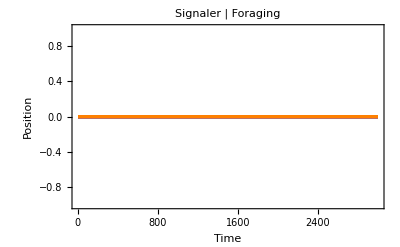

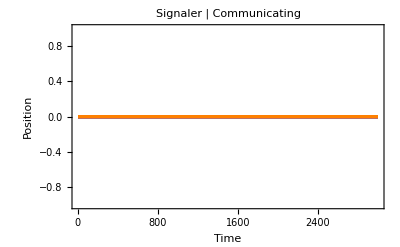

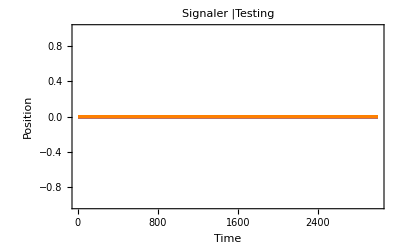

```mathematica
Show[
{ListLinePlot[S1E1P1,PlotStyle->Blue],
ListLinePlot[S1E2P1,PlotStyle->Orange]
},PlotRange->All,Frame->True,FrameLabel->{"Time","Position"},PlotLabel->"Signaler | Foraging"]

Show[
{ListLinePlot[S1E1P2,PlotStyle->Blue],
ListLinePlot[S1E2P2,PlotStyle->Orange]
},PlotRange->All,Frame->True,FrameLabel->{"Time","Position"},PlotLabel->"Signaler | Communicating"]

Show[
{ListLinePlot[S1E1P3,PlotStyle->Blue],
ListLinePlot[S1E2P3,PlotStyle->Orange]
},PlotRange->All,Frame->True,FrameLabel->{"Time","Position"},PlotLabel->"Signaler |Testing"]
```

```mathematica
R1E1P1=Import[d<>"behavior_Receiver_"<>r<>"_Env1_Phase1.dat"];
R1E1P2=Import[d<>"behavior_Receiver_"<>r<>"_Env1_Phase2.dat"];
R1E1P3=Import[d<>"behavior_Receiver_"<>r<>"_Env1_Phase3.dat"];

R1E2P1=Import[d<>"behavior_Receiver_"<>r<>"_Env2_Phase1.dat"];
R1E2P2=Import[d<>"behavior_Receiver_"<>r<>"_Env2_Phase2.dat"];
R1E2P3=Import[d<>"behavior_Receiver_"<>r<>"_Env2_Phase3.dat"];
```

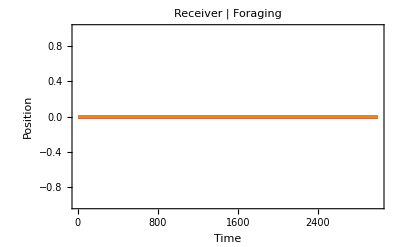

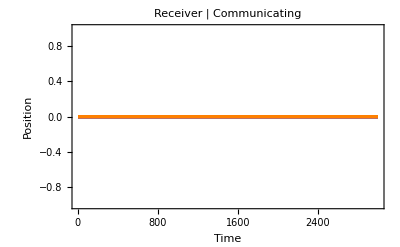

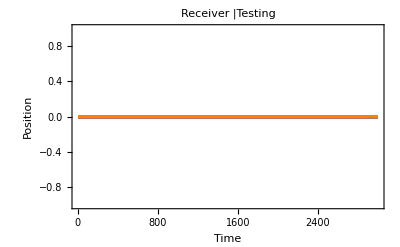

```mathematica
Show[
{ListLinePlot[R1E1P1,PlotStyle->Blue],
ListLinePlot[R1E2P1,PlotStyle->Orange]
},PlotRange->All,Frame->True,FrameLabel->{"Time","Position"},PlotLabel->"Receiver | Foraging"]

Show[
{ListLinePlot[R1E1P2,PlotStyle->Blue],
ListLinePlot[R1E2P2,PlotStyle->Orange]
},PlotRange->All,Frame->True,FrameLabel->{"Time","Position"},PlotLabel->"Receiver | Communicating"]

Show[
{ListLinePlot[R1E1P3,PlotStyle->Blue],
ListLinePlot[R1E2P3,PlotStyle->Orange]
},PlotRange->All,Frame->True,FrameLabel->{"Time","Position"},PlotLabel->"Receiver |Testing"]
```